## Δ Orientation in ℂ

Determining the orientation of a loop through three points in ℂ.

Here is away using the determinant.

0.49607

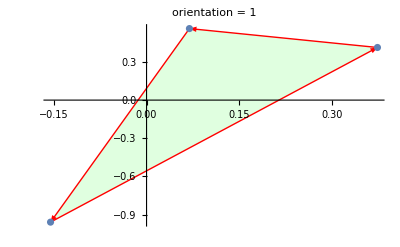

```mathematica
{p1,p2,p3}=RandomComplex[{-1-I,1+I},3];
{u1,u2}={p1,p3}-p2;
orient=-Det[ReIm[{u1,u2}]]
ListPlot[ReIm[{p1,p2,p3}],
Prolog->{
{LightGreen,Polygon[ReIm[{p1,p2,p3}]]},
{Red, Map[Arrow,ReIm[{{p1,p2},{p2,p3},{p3,p1}}]]}
},
PlotLabel->StringForm["orientation = ``",Sign[orient]]]
```

## Hermite Interpolation on a line ∫_a^b f(z)dz

### (0,1) Hermite cubics

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=3;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

### (0,1) Hermite cubics with central node.

On (0,1) the nodal Hermite interpolation polynomials are

```mathematica
Clear[c,x,f,p]
p=5;
f[x_]=Sum[c[i] x^i,{i,0,p}];
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1,f[1/2]==0,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==1,f'[1/2]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==0,f[1/2]==0,f'[1/2]==1}
}];
TabView[{
"f"->Plot[Evaluate[g[x]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

12

### (0,1) Hermite reciprocal cubics

On (0,1) I can use things other than polynomials.  I could use “symmetric” Laurent polynomials
about some point lying off the line.  This does not work!

```mathematica
Clear[c,a,x,f,p]
r=2;
f[x_]=Sum[c[i](x-(1/2+a ⅈ)  )^i ,{i,-r,r}]
Solve[{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0}]
Solve[{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0}]
```

c[-2]/(-1/2-ⅈ a+x)^2+c[-1]/(-1/2-ⅈ a+x)+c[0]+(-1/2-ⅈ a+x) c[1]+(-1/2-ⅈ a+x)^2 c[2]

{{c[-2]→1/16 (1+4 a^2)^2 (2 ⅈ a+c[2]),c[-1]→1/8 (1+4 a^2) (-1+12 a^2-8 ⅈ a c[2]),c[0]→-1/2 ⅈ (ⅈ+a+12 a^3-ⅈ c[2]-12 ⅈ a^2 c[2]),c[1]→1/2 (-1-4 a^2+8 ⅈ a c[2])}}

{{c[-2]→1/32 (1+4 a^2)^2 (1+2 ⅈ a+2 c[2]),c[-1]→1/16 (1+4 a^2) (-1-8 ⅈ a+12 a^2-16 ⅈ a c[2]),c[0]→-1/8 ⅈ (-ⅈ-2 a-20 ⅈ a^2+24 a^3-4 ⅈ c[2]-48 ⅈ a^2 c[2]),c[1]→1/4 (1+4 ⅈ a-4 a^2+16 ⅈ a c[2])}}

```mathematica
g[x_]=Map[Factor[f[x]/.Solve[#]]&,
{
{f[0]==1,f'[0]==0,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==1,f[1]==0,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==1,f'[1]==0},
{f[0]==0,f'[0]==0,f[1]==0,f'[1]==1}
}]
```

{{-(-1+x)^2/(-1+2 x)},(-c[-1]+ⅈ a c[0]-x c[0]+a^2 c[1]+2 ⅈ a x c[1]-x^2 c[1])/(ⅈ a-x),{x^2/(-1+2 x)},(-c[-1]+ⅈ a c[0]-x c[0]+a^2 c[1]+2 ⅈ a x c[1]-x^2 c[1])/(ⅈ a-x)}

```mathematica
TabView[{
"f"->Plot[Evaluate[Re[g[x]]],{x,0,1},PlotLegends->Automatic],
"f'"->Plot[Evaluate[g'[x]],{x,0,1},PlotLegends->Automatic]
}]
```

{1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1]),1/((0.-0.2 ⅈ)+1. x)1. (1. c[-1]-(0.+0.2 ⅈ) c[0]+1. x c[0]-(0.04+0. ⅈ) c[1]-(0.+0.4 ⅈ) x c[1]+1. x^2 c[1])}

12

## Estimating Poles

In practice I have a significant number s m samples from a function with a m poles. The closed contour integral (if evaluated accurately) has a lot fewer poles and we know where they are.

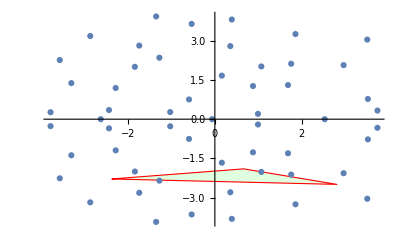

```mathematica
{m,s}={55,4};
{p1,p2,p3}=3RandomComplex[{-1-I,1+I},{3}];
A=RandomReal[{-1,1},{m,m}];
λ=Eigenvalues[A];
ListPlot[ReIm[λ],Prolog->{LightGreen,EdgeForm[Red], Polygon[ReIm[{p1,p2,p3}]]}]
S=Orthogonalize[RandomReal[{-1,1},{s,m}]]ᵀ;
Res[λ_]:=Inverse[A-λ IdentityMatrix[m]]
Clear[F1,F2,F3]
MaxOrder=13;
{F1[0],F2[0],F3[0]}=Map[LinearSolve[A-# IdentityMatrix[m],S]&,{p1,p2,p3}];
Do[
{F1[i],F2[i],F3[i]}={
LinearSolve[A-p1 IdentityMatrix[m],F1[i-1]],
LinearSolve[A-p2 IdentityMatrix[m],F2[i-1]],
LinearSolve[A-p3 IdentityMatrix[m],F3[i-1]]},
{i, 1,MaxOrder}]
```

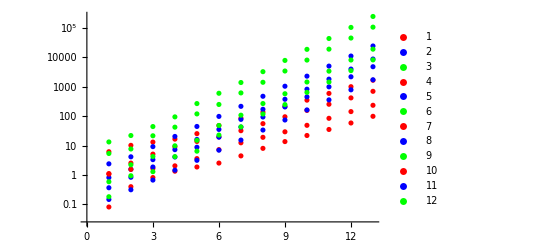

```mathematica
jVal=4;
iVal=5;
ListLogPlot[{
Table[Norm[F1[i]],{i,1,MaxOrder}],
Table[Norm[F2[i]],{i,1,MaxOrder}],
Table[Norm[F3[i]],{i,1,MaxOrder}],
Table[Norm[F1[i]⟦All,jVal⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦All,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦All,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F1[i]⟦iVal,All⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦iVal,All⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦iVal,All⟧],{i,1, MaxOrder}],
Table[Norm[F1[i]⟦iVal,jVal⟧],{i,1, MaxOrder}],Table[Norm[F2[i]⟦iVal,jVal⟧],{i,1, MaxOrder}],
Table[Norm[F3[i]⟦iVal,jVal⟧],{i,1, MaxOrder}]
},
PlotStyle->{Red, Blue, Green},
PlotLegends->Range[1,100]]
```

## Interpolation in Mathematica

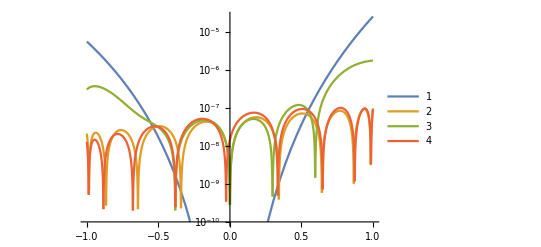

```mathematica
Needs["FunctionApproximations`"]
Clear[m,n,f,p,r,e]
{m,n}={4,4};
f[x_]:=Cos[x] E^x
p[x_]=N[PadeApproximant[f[x],{x,0,{m,n}}]];
r[x_]=RationalInterpolation[f[x],{x,m,n},{x,-1.0,1}];
e[x_]=EconomizedRationalApproximation[f[x],{x,{-1,1},m,n}];
{xs,{mm[x_],err}}=MiniMaxApproximation[f[x],{x,{-1,1},m,n}];
LogPlot[{Abs[f[x]-p[x]],Abs[f[x]-r[x]],Abs[f[x]-e[x]],Abs[f[x]-mm[x]]},{x,-1,1},
PlotLegends->Automatic]
```

```mathematica
?Interpolation
```